=== Three-Body Initial Conditions (Seed 67) ===

Body 1: pos = {0,0}, vel = {0.,1.}

Body 2: pos = {5.62001,2.91992}, vel = {-1.,0.}

Body 3: pos = {-2.08239,12.6573}, vel = {0,0}

System dimension: n = 12

Initial state (positions only):

Body 1: {0, 0}

Body 2: {5.62001, 2.91992}

Body 3: {-2.08239, 12.6573}

=== Testing integration for T = 1.0 ===

Position after t = 1.:

Body 1: {0.0125871, 1.00953}

Body 2: {4.60487, 2.91623}

Body 3: {-2.07984, 12.6515}

Instantaneous λ estimate: 1.01295

=== Starting Lyapunov Computation ===

T = 0.5, dt = 0.1, K = 200

Total integration time: 100.

Iteration 20/200  λ₁ = 0.119011  λ₂ = 0.00693438  Max = 0.139587

Iteration 40/200  λ₁ = 0.0968206  λ₂ = -0.0043877  Max = 0.157085

Iteration 60/200  λ₁ = 0.0752789  λ₂ = 0.0120979  Max = 0.116867

Iteration 80/200  λ₁ = 0.0650777  λ₂ = 0.01434  Max = 0.0956595

Iteration 100/200  λ₁ = 0.0573123  λ₂ = 0.0151748  Max = 0.0811507

Iteration 120/200  λ₁ = 0.0512612  λ₂ = 0.0154639  Max = 0.0703781

Iteration 140/200  λ₁ = 0.0464505  λ₂ = 0.0154434  Max = 0.0620933

Iteration 160/200  λ₁ = 0.042547  λ₂ = 0.0152455  Max = 0.0555507

Iteration 180/200  λ₁ = 0.0393208  λ₂ = 0.0149497  Max = 0.0502676

Iteration 200/200  λ₁ = 0.0366123  λ₂ = 0.0146037  Max = 0.0459204

=== Computation Complete ===

Final Lyapunov Exponents (after 200 iterations):

λ1 = 0.0366123

λ2 = 0.0146037

λ3 = 0.0459204

λ4 = 0.0441291

λ5 = 0.000829565

λ6 = -0.0247747

λ7 = 0.0132606

λ8 = -0.0225176

λ9 = -0.0387072

λ10 = -0.043634

λ11 = -0.0152347

λ12 = -0.0104876

Largest λ (chaos strength): 0.0459204

Number of positive exponents: 5

Sum of λ's (should be ~0 for Hamiltonian): -3.26909×10^-8

✓ SYSTEM IS CHAOTIC (positive Lyapunov exponent > 0.01)

=== Convergence Plot (First 6 Exponents) ===

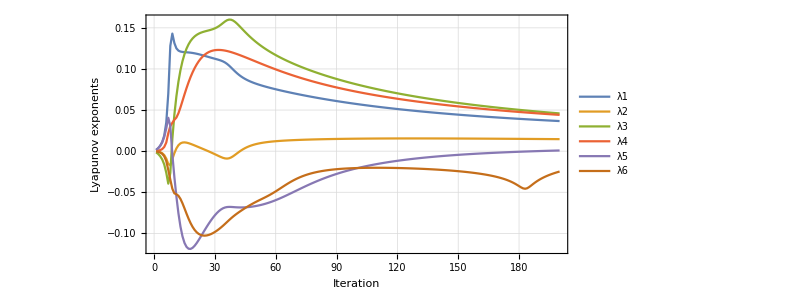

=== Detailed Convergence of Largest Exponent ===

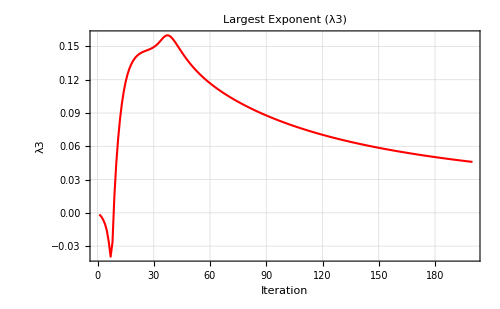

=== Final Lyapunov Spectrum ===

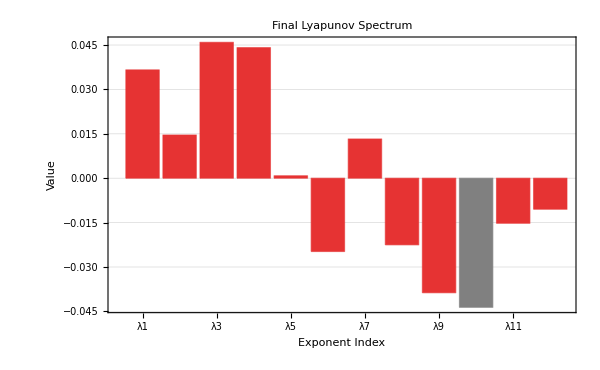

=== Symplectic Symmetry Check ===

λ_i + λ_{n+1-i} (should be near 0):

Pair 1: 0.0261247

Pair 2: -0.000630965

Pair 3: 0.00228644

Pair 4: 0.00542187

Pair 5: -0.021688

Pair 6: -0.011514

Average deviation from 0: 0.0112777

=== Diagnostics ===

Initial energy (kinetic + potential):

E = 0.683602

Variation in last 10 λ₁ values: 0.00116291

⚠ λ₁ still showing significant variation - may need more iterations

```mathematica
(* ==========THREE-BODY LYAPUNOV EXPONENTS==========*)ClearAll["Global`*"];

(* ==========1. UTILITY FUNCTIONS==========*)
JacobianMtx[funs_List,vars_List]:=Outer[D,funs,vars]

RKStep[f_,y_,y0_,dt_]:=Module[{k1,k2,k3,k4},k1=dt N[f/. Thread[y->y0]];
k2=dt N[f/. Thread[y->y0+k1/2]];
k3=dt N[f/. Thread[y->y0+k2/2]];
k4=dt N[f/. Thread[y->y0+k3]];
y0+(k1+2 k2+2 k3+k4)/6]

RKPoint[f_List,y_List,y0_List,{t1_,dt_}]:=Nest[RKStep[f,y,#,N[dt]]&,N[y0],Round[N[t1/dt]]]

IntVarEq[F_List,DPhi_List,x_List,Phi_List,x0_List,Phi0_List,{t1_,dt_}]:=Module[{n,f,y,y0,yt},n=Length[x0];
f=Flatten[Join[F,DPhi]];
y=Flatten[Join[x,Phi]];
y0=Flatten[Join[x0,Phi0]];
yt=Nest[RKStep[f,y,#,N[dt]]&,N[y0],Round[N[t1/dt]]];
{First[#],Rest[#]}&@Partition[yt,n]]

(*Gram-Schmidt functions*)
prj[v1_,v2_]:=(v2.v1) v2/(v2.v2)
multiprj[v1_,vecs_]:=Plus@@Map[prj[v1,#]&,vecs]
GramSchm[vecs_]:=Fold[Join[#1,{#2-multiprj[#2,#1]}]&,{},vecs];

(* ==========2. THREE-BODY SYSTEM DEFINITION==========*)
(*Parameters*)
G=1.0;m1=1.0;m2=1.0;m3=1.0;
conv=0.1;
seed=67;

(*Initial conditions*)
SeedRandom[seed];
pos1={0,0};
vel1={0,10}*conv;
q2x=RandomReal[{5,20}];q2y=RandomReal[{0,10}];
pos2={q2x,q2y};vel2={-10,0}*conv;
q3x=RandomReal[{-10,0}];q3y=RandomReal[{5,20}];
pos3={q3x,q3y};vel3={0,0};

Print["=== Three-Body Initial Conditions (Seed ",seed,") ==="];
Print["Body 1: pos = ",pos1,", vel = ",vel1];
Print["Body 2: pos = ",pos2,", vel = ",vel2];
Print["Body 3: pos = ",pos3,", vel = ",vel3];
Print[""];

(* ==========3. FIRST-ORDER SYSTEM (12D)==========*)
(*Variables:x1,y1,vx1,vy1,x2,y2,vx2,vy2,x3,y3,vx3,vy3*)
x={x1,y1,vx1,vy1,x2,y2,vx2,vy2,x3,y3,vx3,vy3};
n=Length[x];  (*n=12*)

(*Distances for gravitational forces*)
r12=Sqrt[(x2-x1)^2+(y2-y1)^2];
r13=Sqrt[(x3-x1)^2+(y3-y1)^2];
r23=Sqrt[(x3-x2)^2+(y3-y2)^2];

(*Forces with regularization to avoid singularities*)
epsilon=10^-8;
force=1/(#^3+epsilon)&;  (*Regularized 1/r^3*)

(*Equations of motion:dx/dt=v,dv/dt=acceleration*)
F={vx1,(*x1'=vx1*)vy1,(*y1'=vy1*)G*m2*(x2-x1)*force[r12]+G*m3*(x3-x1)*force[r13],(*vx1'*)G*m2*(y2-y1)*force[r12]+G*m3*(y3-y1)*force[r13],(*vy1'*)vx2,(*x2'=vx2*)vy2,(*y2'=vy2*)G*m1*(x1-x2)*force[r12]+G*m3*(x3-x2)*force[r23],(*vx2'*)G*m1*(y1-y2)*force[r12]+G*m3*(y3-y2)*force[r23],(*vy2'*)vx3,(*x3'=vx3*)vy3,(*y3'=vy3*)G*m1*(x1-x3)*force[r13]+G*m2*(x2-x3)*force[r23],(*vx3'*)G*m1*(y1-y3)*force[r13]+G*m2*(y2-y3)*force[r23]   (*vy3'*)};

(* ==========4. JACOBIAN AND VARIATIONAL EQUATIONS==========*)
(*Compute Jacobian matrix symbolically*)
Phi=Array[b,{n,n}];
J=JacobianMtx[F,x];  (*12x12 Jacobian*)
DPhi=Flatten[Phi.Transpose[J]];  (*Variational equations*)

(*Initial conditions*)
x0=Flatten[{pos1,vel1,pos2,vel2,pos3,vel3}];
Phi0=IdentityMatrix[n];

Print["System dimension: n = ",n];
Print["Initial state (positions only):"];
Print["Body 1: {",x0[[1]],", ",x0[[2]],"}"];
Print["Body 2: {",x0[[5]],", ",x0[[6]],"}"];
Print["Body 3: {",x0[[9]],", ",x0[[10]],"}"];
Print[""];

(* ==========5. TEST INTEGRATION==========*)
Print["=== Testing integration for T = 1.0 ==="];
Ttest=1.0;
stepsize=0.1;
{xT,PhiT}=IntVarEq[F,DPhi,x,Phi,x0,Phi0,{Ttest,stepsize}];

Print["Position after t = ",Ttest,":"];
Print["Body 1: {",xT[[1]],", ",xT[[2]],"}"];
Print["Body 2: {",xT[[5]],", ",xT[[6]],"}"];
Print["Body 3: {",xT[[9]],", ",xT[[10]],"}"];

(*Quick Lyapunov test*)
u=Table[RandomReal[],{n}];
instantLambda=Log[Norm[PhiT.u]]/Ttest;
Print["Instantaneous λ estimate: ",instantLambda];
Print[""];

(* ==========6. MAIN LYAPUNOV COMPUTATION==========*)
(*Parameters*)
T=0.5;         (*Reorthonormalization time*)
stepsize=0.1;  (*Integration step*)
K=200;         (*Number of iterations-increased for better convergence*)

Print["=== Starting Lyapunov Computation ==="];
Print["T = ",T,", dt = ",stepsize,", K = ",K];
Print["Total integration time: ",K*T];
Print[""];

(*Initialize*)
PhiT=Phi0;
xT=x0;
s={};  (*Store norms for Gram-Schmidt*)
lambdaHistory={};
cumulativeLogs=Table[0.0,{n}];  (*Initialize cumulative logs*)

Monitor[Do[{xT,PhiT}=IntVarEq[F,DPhi,x,Phi,xT,PhiT,{T,stepsize}];
(*Gram-Schmidt reorthonormalization*)W=GramSchm[PhiT];
norms=Map[Norm,W];
(*Store norms*)s=Append[s,norms];
(*Reorthonormalize PhiT*)PhiT=W/norms;
(*Update cumulative logs and compute current LCEs*)cumulativeLogs=cumulativeLogs+Log[norms];
currentLCEs=cumulativeLogs/(i*T);(*i iterations of length T*)AppendTo[lambdaHistory,currentLCEs];
(*Progress*)If[Mod[i,20]==0,Print["Iteration ",i,"/",K,"  λ₁ = ",currentLCEs[[1]],"  λ₂ = ",currentLCEs[[2]],"  Max = ",Max[currentLCEs]]];,{i,K}],ProgressIndicator[i,{1,K}]];

Print[""];
Print["=== Computation Complete ==="];

(* ==========7. FINAL RESULTS==========*)
finalLCEs=Last[lambdaHistory];
Print["\nFinal Lyapunov Exponents (after ",K," iterations):"];
For[i=1,i<=Min[12,Length[finalLCEs]],i++,Print["λ",i," = ",finalLCEs[[i]]]];

Print[""];
Print["Largest λ (chaos strength): ",Max[finalLCEs]];
Print["Number of positive exponents: ",Count[finalLCEs,x_/;x>0.001]];
Print["Sum of λ's (should be ~0 for Hamiltonian): ",Total[finalLCEs]];

(*Check for chaos*)
maxLCE=Max[finalLCEs];
If[maxLCE>0.01,Print["\n✓ SYSTEM IS CHAOTIC (positive Lyapunov exponent > 0.01)"],If[maxLCE>0,Print["\n⚠ System shows weak chaos (positive but small exponent)"],Print["\n✗ System appears regular (no positive exponent)"]]];

(* ==========8. PLOTTING==========*)
(*8.1 Convergence plot of first 6 exponents*)
Print["\n=== Convergence Plot (First 6 Exponents) ==="];
If[Length[lambdaHistory]>0,convData=Transpose[lambdaHistory][[1;;6]];(*First 6 exponents*)

convPlot=ListLinePlot[convData,PlotLegends->Placed[LineLegend[Table[Style["λ"<>ToString[i],FontSize->12],{i,6}],LegendFunction->(Framed[#,RoundingRadius->0]&)],Right],Frame->True,FrameStyle->Directive[Black,Thickness[0.002]],FrameLabel->{Style["Iteration",Italic,FontSize->14],Style["Lyapunov exponents",Italic,FontSize->14]},GridLines->Automatic,GridLinesStyle->LightGray,ImageSize->600,AspectRatio->1/2,PlotRange->{{0,200},All}];


Print[convPlot];];



(*8.2 Detailed convergence of largest exponent*)
Print["\n=== Detailed Convergence of Largest Exponent ==="];
largestIndex=First[Ordering[finalLCEs,-1]];
largestExpData=Transpose[lambdaHistory][[largestIndex]];
plotLargest=ListPlot[largestExpData,Joined->True,Frame->True,FrameLabel->{"Iteration","λ"<>ToString[largestIndex]},PlotLabel->Style["Largest Exponent (λ"<>ToString[largestIndex]<>")",14],GridLines->Automatic,ImageSize->500,PlotStyle->{Red,Thickness[0.003]}];
Print[plotLargest];

(*8.3 Final spectrum bar chart*)
Print["\n=== Final Lyapunov Spectrum ==="];
spectrumPlot=BarChart[finalLCEs,ChartLabels->Table["λ"<>ToString[i],{i,Length[finalLCEs]}],Frame->True,FrameLabel->{"Exponent Index","Value"},PlotLabel->Style["Final Lyapunov Spectrum",16,Bold],GridLines->Automatic,ImageSize->600,ColorFunction->Function[{height},If[height>0.001,RGBColor[0.9,0.2,0.2],If[height<-0.001,RGBColor[0.2,0.2,0.9],RGBColor[0.5,0.5,0.5]]]],ChartStyle->"TemperatureMap"];
Print[spectrumPlot];

(*8.4 Symplectic symmetry check:λ_i+λ_{n+1-i} should be~0*)
Print["\n=== Symplectic Symmetry Check ==="];
If[EvenQ[n],sympPairs=Table[finalLCEs[[i]]+finalLCEs[[n+1-i]],{i,n/2}];
Print["λ_i + λ_{n+1-i} (should be near 0):"];
For[i=1,i<=Length[sympPairs],i++,Print["Pair ",i,": ",sympPairs[[i]]]];
Print["Average deviation from 0: ",Mean[Abs[sympPairs]]];];


(*
(*8.5 Trajectory plot (optional)*)
Print["\n=== Optional: Short Trajectory Plot ==="];
trajSteps=1000;
trajDT=0.01;
trajPoints=NestList[RKStep[F,x,#,trajDT]&,x0,trajSteps];
traj1=trajPoints[[All,{1,2}]];
traj2=trajPoints[[All,{5,6}]];
traj3=trajPoints[[All,{9,10}]];

trajPlot=ListLinePlot[{traj1,traj2,traj3},PlotStyle->{{Blue,Thickness[0.002]},{Red,Thickness[0.002]},{Green,Thickness[0.002]}},Frame->True,FrameLabel->{"x","y"},PlotLabel->Style["Trajectories (first "<>ToString[trajSteps*trajDT]<>" time units)",14],AspectRatio->1,ImageSize->500,PlotLegends->{"Body 1","Body 2","Body 3"}];
Print[trajPlot];


*)

(* ==========9. DIAGNOSTICS==========*)
Print["\n=== Diagnostics ==="];
Print["Initial energy (kinetic + potential):"];
(*Compute initial energy*)
r12init=Norm[pos2-pos1];
r13init=Norm[pos3-pos1];
r23init=Norm[pos3-pos2];
kinetic=0.5*m1*Norm[vel1]^2+0.5*m2*Norm[vel2]^2+0.5*m3*Norm[vel3]^2;
potential=-G*(m1*m2/r12init+m1*m3/r13init+m2*m3/r23init);
energyInit=kinetic+potential;
Print["E = ",energyInit];

(*Check if exponents are converging*)
If[Length[lambdaHistory]>10,lastValues=Take[Transpose[lambdaHistory][[1]],-10];
variation=Max[lastValues]-Min[lastValues];
Print["Variation in last 10 λ₁ values: ",variation];
If[variation<0.01*Abs[Mean[lastValues]],Print["✓ λ₁ appears to be converging"],Print["⚠ λ₁ still showing significant variation - may need more iterations"]];];
```

=== Three-Body Initial Conditions (Seed 12) ===

Body 1: pos = {0,0}, vel = {0.,1.}

Body 2: pos = {7.11204,0.364441}, vel = {-1.,0.}

Body 3: pos = {-4.78589,10.9432}, vel = {0,0}

System dimension: n = 12

Initial state (positions only):

Body 1: {0, 0}

Body 2: {7.11204, 0.364441}

Body 3: {-4.78589, 10.9432}

=== Testing integration for T = 1.0 ===

Position after t = 1.:

Body 1: {0.00939184, 1.00337}

Body 2: {6.09962, 0.365809}

Body 3: {-4.78287, 10.9385}

Instantaneous λ estimate: 1.08943

=== Starting Lyapunov Computation ===

T = 0.5, dt = 0.1, K = 200

Total integration time: 100.

Iteration 20/200  λ₁ = 0.0354828  λ₂ = 0.00157479  Max = 0.0852226

Iteration 40/200  λ₁ = 0.0496677  λ₂ = 0.00173306  Max = 0.104301

Iteration 60/200  λ₁ = 0.0433531  λ₂ = 0.0104624  Max = 0.0940875

Iteration 80/200  λ₁ = 0.038191  λ₂ = 0.0138775  Max = 0.0817845

Iteration 100/200  λ₁ = 0.0342137  λ₂ = 0.0150671  Max = 0.0722869

Iteration 120/200  λ₁ = 0.0310721  λ₂ = 0.0153226  Max = 0.0647325

Iteration 140/200  λ₁ = 0.0285254  λ₂ = 0.0151646  Max = 0.0585894

Iteration 160/200  λ₁ = 0.0264153  λ₂ = 0.0148207  Max = 0.0535319

Iteration 180/200  λ₁ = 0.024635  λ₂ = 0.0143973  Max = 0.049308

Iteration 200/200  λ₁ = 0.02311  λ₂ = 0.0139466  Max = 0.0457316

=== Computation Complete ===

Final Lyapunov Exponents (after 200 iterations):

λ1 = 0.02311

λ2 = 0.0139466

λ3 = 0.0457316

λ4 = 0.0446425

λ5 = 0.000167362

λ6 = 0.00188814

λ7 = -0.00224566

λ8 = -0.00998685

λ9 = -0.0408905

λ10 = -0.0438964

λ11 = -0.0224508

λ12 = -0.010016

Largest λ (chaos strength): 0.0457316

Number of positive exponents: 5

Sum of λ's (should be ~0 for Hamiltonian): -6.26998×10^-12

✓ SYSTEM IS CHAOTIC (positive Lyapunov exponent > 0.01)

=== Convergence Plot (First 6 Exponents) ===

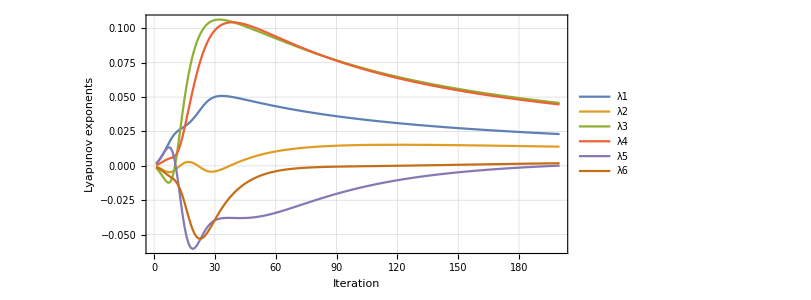

=== Detailed Convergence of Largest Exponent ===

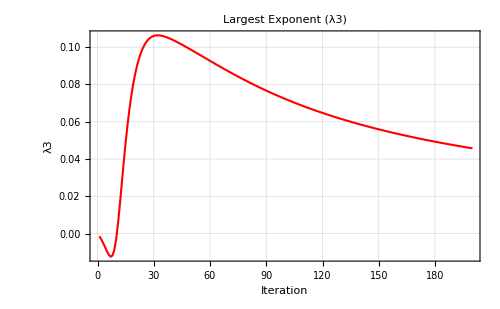

=== Final Lyapunov Spectrum ===

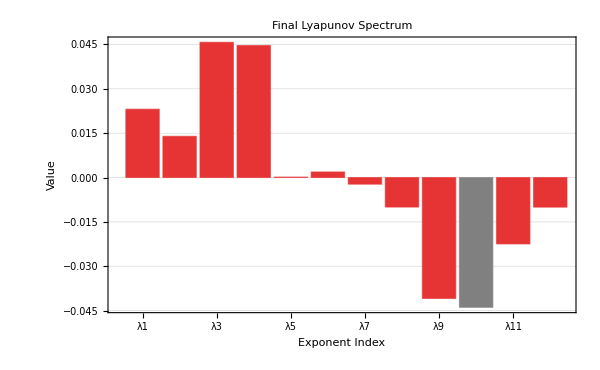

=== Symplectic Symmetry Check ===

λ_i + λ_{n+1-i} (should be near 0):

Pair 1: 0.0130941

Pair 2: -0.00850424

Pair 3: 0.00183523

Pair 4: 0.00375196

Pair 5: -0.00981949

Pair 6: -0.000357519

Average deviation from 0: 0.00622708

=== Diagnostics ===

Initial energy (kinetic + potential):

E = 0.713043

Variation in last 10 λ₁ values: 0.000658439

⚠ λ₁ still showing significant variation - may need more iterations

```mathematica
(* ==========THREE-BODY LYAPUNOV EXPONENTS==========*)ClearAll["Global`*"];

(* ==========1. UTILITY FUNCTIONS==========*)
JacobianMtx[funs_List,vars_List]:=Outer[D,funs,vars]

RKStep[f_,y_,y0_,dt_]:=Module[{k1,k2,k3,k4},k1=dt N[f/. Thread[y->y0]];
k2=dt N[f/. Thread[y->y0+k1/2]];
k3=dt N[f/. Thread[y->y0+k2/2]];
k4=dt N[f/. Thread[y->y0+k3]];
y0+(k1+2 k2+2 k3+k4)/6]

RKPoint[f_List,y_List,y0_List,{t1_,dt_}]:=Nest[RKStep[f,y,#,N[dt]]&,N[y0],Round[N[t1/dt]]]

IntVarEq[F_List,DPhi_List,x_List,Phi_List,x0_List,Phi0_List,{t1_,dt_}]:=Module[{n,f,y,y0,yt},n=Length[x0];
f=Flatten[Join[F,DPhi]];
y=Flatten[Join[x,Phi]];
y0=Flatten[Join[x0,Phi0]];
yt=Nest[RKStep[f,y,#,N[dt]]&,N[y0],Round[N[t1/dt]]];
{First[#],Rest[#]}&@Partition[yt,n]]

(*Gram-Schmidt functions*)
prj[v1_,v2_]:=(v2.v1) v2/(v2.v2)
multiprj[v1_,vecs_]:=Plus@@Map[prj[v1,#]&,vecs]
GramSchm[vecs_]:=Fold[Join[#1,{#2-multiprj[#2,#1]}]&,{},vecs];

(* ==========2. THREE-BODY SYSTEM DEFINITION==========*)
(*Parameters*)
G=1.0;m1=1.0;m2=1.0;m3=1.0;
conv=0.1;
seed=12;

(*Initial conditions*)
SeedRandom[seed];
pos1={0,0};
vel1={0,10}*conv;
q2x=RandomReal[{5,20}];q2y=RandomReal[{0,10}];
pos2={q2x,q2y};vel2={-10,0}*conv;
q3x=RandomReal[{-10,0}];q3y=RandomReal[{5,20}];
pos3={q3x,q3y};vel3={0,0};

Print["=== Three-Body Initial Conditions (Seed ",seed,") ==="];
Print["Body 1: pos = ",pos1,", vel = ",vel1];
Print["Body 2: pos = ",pos2,", vel = ",vel2];
Print["Body 3: pos = ",pos3,", vel = ",vel3];
Print[""];

(* ==========3. FIRST-ORDER SYSTEM (12D)==========*)
(*Variables:x1,y1,vx1,vy1,x2,y2,vx2,vy2,x3,y3,vx3,vy3*)
x={x1,y1,vx1,vy1,x2,y2,vx2,vy2,x3,y3,vx3,vy3};
n=Length[x];  (*n=12*)

(*Distances for gravitational forces*)
r12=Sqrt[(x2-x1)^2+(y2-y1)^2];
r13=Sqrt[(x3-x1)^2+(y3-y1)^2];
r23=Sqrt[(x3-x2)^2+(y3-y2)^2];

(*Forces with regularization to avoid singularities*)
epsilon=10^-8;
force=1/(#^3+epsilon)&;  (*Regularized 1/r^3*)

(*Equations of motion:dx/dt=v,dv/dt=acceleration*)
F={vx1,(*x1'=vx1*)vy1,(*y1'=vy1*)G*m2*(x2-x1)*force[r12]+G*m3*(x3-x1)*force[r13],(*vx1'*)G*m2*(y2-y1)*force[r12]+G*m3*(y3-y1)*force[r13],(*vy1'*)vx2,(*x2'=vx2*)vy2,(*y2'=vy2*)G*m1*(x1-x2)*force[r12]+G*m3*(x3-x2)*force[r23],(*vx2'*)G*m1*(y1-y2)*force[r12]+G*m3*(y3-y2)*force[r23],(*vy2'*)vx3,(*x3'=vx3*)vy3,(*y3'=vy3*)G*m1*(x1-x3)*force[r13]+G*m2*(x2-x3)*force[r23],(*vx3'*)G*m1*(y1-y3)*force[r13]+G*m2*(y2-y3)*force[r23]   (*vy3'*)};

(* ==========4. JACOBIAN AND VARIATIONAL EQUATIONS==========*)
(*Compute Jacobian matrix symbolically*)
Phi=Array[b,{n,n}];
J=JacobianMtx[F,x];  (*12x12 Jacobian*)
DPhi=Flatten[Phi.Transpose[J]];  (*Variational equations*)

(*Initial conditions*)
x0=Flatten[{pos1,vel1,pos2,vel2,pos3,vel3}];
Phi0=IdentityMatrix[n];

Print["System dimension: n = ",n];
Print["Initial state (positions only):"];
Print["Body 1: {",x0[[1]],", ",x0[[2]],"}"];
Print["Body 2: {",x0[[5]],", ",x0[[6]],"}"];
Print["Body 3: {",x0[[9]],", ",x0[[10]],"}"];
Print[""];

(* ==========5. TEST INTEGRATION==========*)
Print["=== Testing integration for T = 1.0 ==="];
Ttest=1.0;
stepsize=0.1;
{xT,PhiT}=IntVarEq[F,DPhi,x,Phi,x0,Phi0,{Ttest,stepsize}];

Print["Position after t = ",Ttest,":"];
Print["Body 1: {",xT[[1]],", ",xT[[2]],"}"];
Print["Body 2: {",xT[[5]],", ",xT[[6]],"}"];
Print["Body 3: {",xT[[9]],", ",xT[[10]],"}"];

(*Quick Lyapunov test*)
u=Table[RandomReal[],{n}];
instantLambda=Log[Norm[PhiT.u]]/Ttest;
Print["Instantaneous λ estimate: ",instantLambda];
Print[""];

(* ==========6. MAIN LYAPUNOV COMPUTATION==========*)
(*Parameters*)
T=0.5;         (*Reorthonormalization time*)
stepsize=0.1;  (*Integration step*)
K=200;         (*Number of iterations-increased for better convergence*)

Print["=== Starting Lyapunov Computation ==="];
Print["T = ",T,", dt = ",stepsize,", K = ",K];
Print["Total integration time: ",K*T];
Print[""];

(*Initialize*)
PhiT=Phi0;
xT=x0;
s={};  (*Store norms for Gram-Schmidt*)
lambdaHistory={};
cumulativeLogs=Table[0.0,{n}];  (*Initialize cumulative logs*)

Monitor[Do[{xT,PhiT}=IntVarEq[F,DPhi,x,Phi,xT,PhiT,{T,stepsize}];
(*Gram-Schmidt reorthonormalization*)W=GramSchm[PhiT];
norms=Map[Norm,W];
(*Store norms*)s=Append[s,norms];
(*Reorthonormalize PhiT*)PhiT=W/norms;
(*Update cumulative logs and compute current LCEs*)cumulativeLogs=cumulativeLogs+Log[norms];
currentLCEs=cumulativeLogs/(i*T);(*i iterations of length T*)AppendTo[lambdaHistory,currentLCEs];
(*Progress*)If[Mod[i,20]==0,Print["Iteration ",i,"/",K,"  λ₁ = ",currentLCEs[[1]],"  λ₂ = ",currentLCEs[[2]],"  Max = ",Max[currentLCEs]]];,{i,K}],ProgressIndicator[i,{1,K}]];

Print[""];
Print["=== Computation Complete ==="];

(* ==========7. FINAL RESULTS==========*)
finalLCEs=Last[lambdaHistory];
Print["\nFinal Lyapunov Exponents (after ",K," iterations):"];
For[i=1,i<=Min[12,Length[finalLCEs]],i++,Print["λ",i," = ",finalLCEs[[i]]]];

Print[""];
Print["Largest λ (chaos strength): ",Max[finalLCEs]];
Print["Number of positive exponents: ",Count[finalLCEs,x_/;x>0.001]];
Print["Sum of λ's (should be ~0 for Hamiltonian): ",Total[finalLCEs]];

(*Check for chaos*)
maxLCE=Max[finalLCEs];
If[maxLCE>0.01,Print["\n✓ SYSTEM IS CHAOTIC (positive Lyapunov exponent > 0.01)"],If[maxLCE>0,Print["\n⚠ System shows weak chaos (positive but small exponent)"],Print["\n✗ System appears regular (no positive exponent)"]]];

(* ==========8. PLOTTING==========*)
(*8.1 Convergence plot of first 6 exponents*)
Print["\n=== Convergence Plot (First 6 Exponents) ==="];
If[Length[lambdaHistory]>0,convData=Transpose[lambdaHistory][[1;;6]];(*First 6 exponents*)convPlot=ListLinePlot[convData,PlotLegends->Placed[LineLegend[Table[Style["λ"<>ToString[i],FontSize->12],{i,6}],LegendFunction->(Framed[#,RoundingRadius->0]&)],Right],Frame->True,FrameStyle->Directive[Black,Thickness[0.002]],FrameLabel->{Style["Iteration",Italic,FontSize->14],Style["Lyapunov exponents",Italic,FontSize->14]},GridLines->Automatic,GridLinesStyle->LightGray,ImageSize->600,AspectRatio->1/2,PlotRange->{{0,200},All}];

Print[convPlot];];

(*8.2 Detailed convergence of largest exponent*)
Print["\n=== Detailed Convergence of Largest Exponent ==="];
largestIndex=First[Ordering[finalLCEs,-1]];
largestExpData=Transpose[lambdaHistory][[largestIndex]];
plotLargest=ListPlot[largestExpData,Joined->True,Frame->True,FrameLabel->{"Iteration","λ"<>ToString[largestIndex]},PlotLabel->Style["Largest Exponent (λ"<>ToString[largestIndex]<>")",14],GridLines->Automatic,ImageSize->500,PlotStyle->{Red,Thickness[0.003]}];
Print[plotLargest];

(*8.3 Final spectrum bar chart*)
Print["\n=== Final Lyapunov Spectrum ==="];
spectrumPlot=BarChart[finalLCEs,ChartLabels->Table["λ"<>ToString[i],{i,Length[finalLCEs]}],Frame->True,FrameLabel->{"Exponent Index","Value"},PlotLabel->Style["Final Lyapunov Spectrum",16,Bold],GridLines->Automatic,ImageSize->600,ColorFunction->Function[{height},If[height>0.001,RGBColor[0.9,0.2,0.2],If[height<-0.001,RGBColor[0.2,0.2,0.9],RGBColor[0.5,0.5,0.5]]]],ChartStyle->"TemperatureMap"];
Print[spectrumPlot];

(*8.4 Symplectic symmetry check:λ_i+λ_{n+1-i} should be~0*)
Print["\n=== Symplectic Symmetry Check ==="];
If[EvenQ[n],sympPairs=Table[finalLCEs[[i]]+finalLCEs[[n+1-i]],{i,n/2}];
Print["λ_i + λ_{n+1-i} (should be near 0):"];
For[i=1,i<=Length[sympPairs],i++,Print["Pair ",i,": ",sympPairs[[i]]]];
Print["Average deviation from 0: ",Mean[Abs[sympPairs]]];];


(*
(*8.5 Trajectory plot (optional)*)
Print["\n=== Optional: Short Trajectory Plot ==="];
trajSteps=1000;
trajDT=0.01;
trajPoints=NestList[RKStep[F,x,#,trajDT]&,x0,trajSteps];
traj1=trajPoints[[All,{1,2}]];
traj2=trajPoints[[All,{5,6}]];
traj3=trajPoints[[All,{9,10}]];

trajPlot=ListLinePlot[{traj1,traj2,traj3},PlotStyle->{{Blue,Thickness[0.002]},{Red,Thickness[0.002]},{Green,Thickness[0.002]}},Frame->True,FrameLabel->{"x","y"},PlotLabel->Style["Trajectories (first "<>ToString[trajSteps*trajDT]<>" time units)",14],AspectRatio->1,ImageSize->500,PlotLegends->{"Body 1","Body 2","Body 3"}];
Print[trajPlot];


*)

(* ==========9. DIAGNOSTICS==========*)
Print["\n=== Diagnostics ==="];
Print["Initial energy (kinetic + potential):"];
(*Compute initial energy*)
r12init=Norm[pos2-pos1];
r13init=Norm[pos3-pos1];
r23init=Norm[pos3-pos2];
kinetic=0.5*m1*Norm[vel1]^2+0.5*m2*Norm[vel2]^2+0.5*m3*Norm[vel3]^2;
potential=-G*(m1*m2/r12init+m1*m3/r13init+m2*m3/r23init);
energyInit=kinetic+potential;
Print["E = ",energyInit];

(*Check if exponents are converging*)
If[Length[lambdaHistory]>10,lastValues=Take[Transpose[lambdaHistory][[1]],-10];
variation=Max[lastValues]-Min[lastValues];
Print["Variation in last 10 λ₁ values: ",variation];
If[variation<0.01*Abs[Mean[lastValues]],Print["✓ λ₁ appears to be converging"],Print["⚠ λ₁ still showing significant variation - may need more iterations"]];];
```

=== STABLE Circular Restricted Configuration ===

Mass ratio: 0.5

Separation: 1.

Angular velocity ω: 1.41421

Body 1 (m1): pos = {-0.5,0}, vel = {0.,0.707107}

Body 2 (m2): pos = {0.5,0}, vel = {0.,-0.707107}

Body 3 (m3 at L4): pos = {0.,0.866025}, vel = {-1.22474,0.}

System dimension: n = 12

Initial state (positions only):

Body 1: {-0.5, 0}

Body 2: {0.5, 0}

Body 3: {0., 0.866025}

=== Testing integration for T = 1.0 ===

Position after t = 1.:

Body 1: {-0.0788599, 0.494839}

Body 2: {0.0777368, -0.493626}

Body 3: {-0.101595, -0.347374}

Instantaneous λ estimate: 2.10122

=== Starting Lyapunov Computation ===

T = 0.5, dt = 0.1, K = 100

Total integration time: 50.

Iteration 20/100  λ₁ = 0.968141  λ₂ = 1.08176  Max = 1.08176

Iteration 40/100  λ₁ = 0.521338  λ₂ = 0.57815  Max = 0.57815

Iteration 60/100  λ₁ = 0.361658  λ₂ = 0.399533  Max = 0.399533

Iteration 80/100  λ₁ = 0.278655  λ₂ = 0.307061  Max = 0.307061

Iteration 100/100  λ₁ = 0.227492  λ₂ = 0.250217  Max = 0.250217

=== Computation Complete ===

Final Lyapunov Exponents (after 100 iterations):

λ1 = 0.227492

λ2 = 0.250217

λ3 = 0.100636

λ4 = 0.0745284

λ5 = 0.055681

λ6 = -0.033886

λ7 = -0.0339366

λ8 = 0.0066708

λ9 = -0.0895252

λ10 = -0.108849

λ11 = -0.124748

λ12 = -0.230022

Largest λ (chaos strength): 0.250217

Number of positive exponents: 6

Sum of λ's (should be ~0 for Hamiltonian): 0.0942586

✓ SYSTEM IS CHAOTIC (positive Lyapunov exponent > 0.01)

=== Convergence Plot (First 6 Exponents) ===

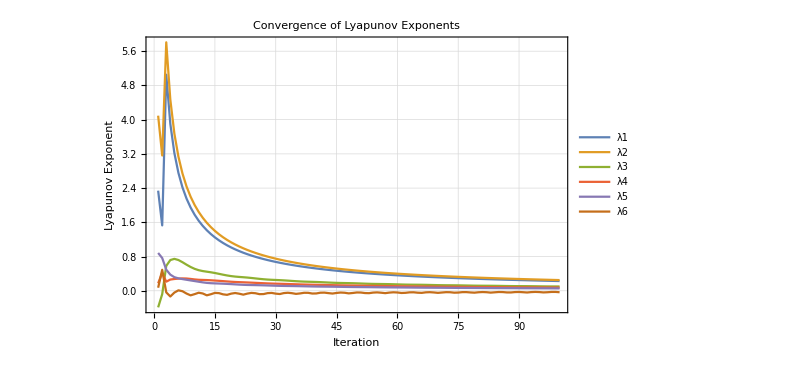

=== Detailed Convergence of Largest Exponent ===

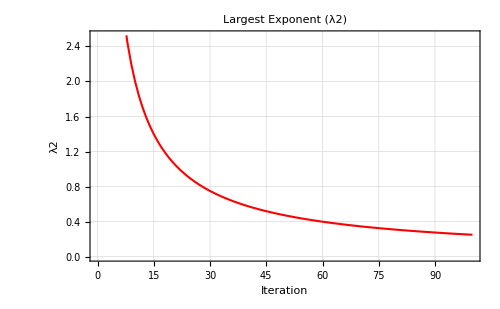

=== Final Lyapunov Spectrum ===

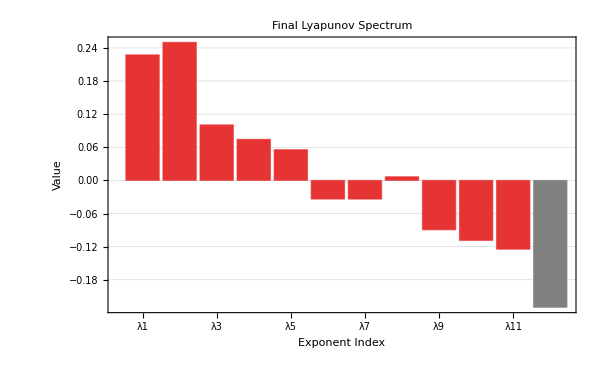

=== Symplectic Symmetry Check ===

λ_i + λ_{n+1-i} (should be near 0):

Pair 1: -0.00253031

Pair 2: 0.125469

Pair 3: -0.00821226

Pair 4: -0.0149969

Pair 5: 0.0623518

Pair 6: -0.0678226

Average deviation from 0: 0.0468971

=== Diagnostics ===

Initial energy (kinetic + potential):

E = -0.50125

Variation in last 10 λ₁ values: 0.0203807

⚠ λ₁ still showing significant variation - may need more iterations

```mathematica
(* ==========THREE-BODY LYAPUNOV EXPONENTS==========*)ClearAll["Global`*"];

(* ==========1. UTILITY FUNCTIONS==========*)
JacobianMtx[funs_List,vars_List]:=Outer[D,funs,vars]

RKStep[f_,y_,y0_,dt_]:=Module[{k1,k2,k3,k4},k1=dt N[f/. Thread[y->y0]];
k2=dt N[f/. Thread[y->y0+k1/2]];
k3=dt N[f/. Thread[y->y0+k2/2]];
k4=dt N[f/. Thread[y->y0+k3]];
y0+(k1+2 k2+2 k3+k4)/6]

RKPoint[f_List,y_List,y0_List,{t1_,dt_}]:=Nest[RKStep[f,y,#,N[dt]]&,N[y0],Round[N[t1/dt]]]

IntVarEq[F_List,DPhi_List,x_List,Phi_List,x0_List,Phi0_List,{t1_,dt_}]:=Module[{n,f,y,y0,yt},n=Length[x0];
f=Flatten[Join[F,DPhi]];
y=Flatten[Join[x,Phi]];
y0=Flatten[Join[x0,Phi0]];
yt=Nest[RKStep[f,y,#,N[dt]]&,N[y0],Round[N[t1/dt]]];
{First[#],Rest[#]}&@Partition[yt,n]]

(*Gram-Schmidt functions*)
prj[v1_,v2_]:=(v2.v1) v2/(v2.v2)
multiprj[v1_,vecs_]:=Plus@@Map[prj[v1,#]&,vecs]
GramSchm[vecs_]:=Fold[Join[#1,{#2-multiprj[#2,#1]}]&,{},vecs];



(* ==========2. THREE-BODY SYSTEM DEFINITION==========*)(*Parameters*)G=1.0;m1=1.0;m2=1.0;m3=0.001;  (*Third body very small*)
conv=1.0;
seed=67;

(*Initial conditions for STABLE circular restricted three-body*)
(*Two massive bodies in circular orbit around COM*)
massRatio=m2/(m1+m2);
distance=1.0;  (*Separation between m1 and m2*)

(*Positions:m1 and m2 in circular orbit,m3 at Lagrange point L4*)
pos1={-distance*massRatio,0};  (*Primary*)
pos2={distance*(1-massRatio),0};  (*Secondary*)

(*Circular velocities for m1 and m2*)
ω=Sqrt[G*(m1+m2)/(distance^3)];
vel1={0,-ω*pos1[[1]]};  (*v=ω×r*)
vel2={0,-ω*pos2[[1]]};

(*m3 at Lagrange point L4 (equilateral triangle)*)
pos3={(pos1[[1]]+pos2[[1]])/2,distance*Sqrt[3]/2};
vel3={-ω*(pos3[[2]]),ω*(pos3[[1]])};  (*Corotating with the system*)

(*Scale if needed*)
vel1=vel1*conv;
vel2=vel2*conv;
vel3=vel3*conv;

Print["=== STABLE Circular Restricted Configuration ==="];
Print["Mass ratio: ",massRatio];
Print["Separation: ",distance];
Print["Angular velocity ω: ",ω];
Print["Body 1 (m1): pos = ",pos1,", vel = ",vel1];
Print["Body 2 (m2): pos = ",pos2,", vel = ",vel2];
Print["Body 3 (m3 at L4): pos = ",pos3,", vel = ",vel3];
Print[""];

(* ==========3. FIRST-ORDER SYSTEM (12D)==========*)
(*Variables:x1,y1,vx1,vy1,x2,y2,vx2,vy2,x3,y3,vx3,vy3*)
x={x1,y1,vx1,vy1,x2,y2,vx2,vy2,x3,y3,vx3,vy3};
n=Length[x];  (*n=12*)

(*Distances for gravitational forces*)
r12=Sqrt[(x2-x1)^2+(y2-y1)^2];
r13=Sqrt[(x3-x1)^2+(y3-y1)^2];
r23=Sqrt[(x3-x2)^2+(y3-y2)^2];

(*Forces with regularization to avoid singularities*)
epsilon=10^-8;
force=1/(#^3+epsilon)&;  (*Regularized 1/r^3*)

(*Equations of motion:dx/dt=v,dv/dt=acceleration*)
F={vx1,(*x1'=vx1*)vy1,(*y1'=vy1*)G*m2*(x2-x1)*force[r12]+G*m3*(x3-x1)*force[r13],(*vx1'*)G*m2*(y2-y1)*force[r12]+G*m3*(y3-y1)*force[r13],(*vy1'*)vx2,(*x2'=vx2*)vy2,(*y2'=vy2*)G*m1*(x1-x2)*force[r12]+G*m3*(x3-x2)*force[r23],(*vx2'*)G*m1*(y1-y2)*force[r12]+G*m3*(y3-y2)*force[r23],(*vy2'*)vx3,(*x3'=vx3*)vy3,(*y3'=vy3*)G*m1*(x1-x3)*force[r13]+G*m2*(x2-x3)*force[r23],(*vx3'*)G*m1*(y1-y3)*force[r13]+G*m2*(y2-y3)*force[r23]   (*vy3'*)};

(* ==========4. JACOBIAN AND VARIATIONAL EQUATIONS==========*)
(*Compute Jacobian matrix symbolically*)
Phi=Array[b,{n,n}];
J=JacobianMtx[F,x];  (*12x12 Jacobian*)
DPhi=Flatten[Phi.Transpose[J]];  (*Variational equations*)

(*Initial conditions*)
x0=Flatten[{pos1,vel1,pos2,vel2,pos3,vel3}];
Phi0=IdentityMatrix[n];

Print["System dimension: n = ",n];
Print["Initial state (positions only):"];
Print["Body 1: {",x0[[1]],", ",x0[[2]],"}"];
Print["Body 2: {",x0[[5]],", ",x0[[6]],"}"];
Print["Body 3: {",x0[[9]],", ",x0[[10]],"}"];
Print[""];

(* ==========5. TEST INTEGRATION==========*)
Print["=== Testing integration for T = 1.0 ==="];
Ttest=1.0;
stepsize=0.1;
{xT,PhiT}=IntVarEq[F,DPhi,x,Phi,x0,Phi0,{Ttest,stepsize}];

Print["Position after t = ",Ttest,":"];
Print["Body 1: {",xT[[1]],", ",xT[[2]],"}"];
Print["Body 2: {",xT[[5]],", ",xT[[6]],"}"];
Print["Body 3: {",xT[[9]],", ",xT[[10]],"}"];

(*Quick Lyapunov test*)
u=Table[RandomReal[],{n}];
instantLambda=Log[Norm[PhiT.u]]/Ttest;
Print["Instantaneous λ estimate: ",instantLambda];
Print[""];

(* ==========6. MAIN LYAPUNOV COMPUTATION==========*)
(*Parameters*)
T=0.5;         (*Reorthonormalization time*)
stepsize=0.1;  (*Integration step*)
K=100;         (*Number of iterations-increased for better convergence*)

Print["=== Starting Lyapunov Computation ==="];
Print["T = ",T,", dt = ",stepsize,", K = ",K];
Print["Total integration time: ",K*T];
Print[""];

(*Initialize*)
PhiT=Phi0;
xT=x0;
s={};  (*Store norms for Gram-Schmidt*)
lambdaHistory={};
cumulativeLogs=Table[0.0,{n}];  (*Initialize cumulative logs*)

Monitor[Do[{xT,PhiT}=IntVarEq[F,DPhi,x,Phi,xT,PhiT,{T,stepsize}];
(*Gram-Schmidt reorthonormalization*)W=GramSchm[PhiT];
norms=Map[Norm,W];
(*Store norms*)s=Append[s,norms];
(*Reorthonormalize PhiT*)PhiT=W/norms;
(*Update cumulative logs and compute current LCEs*)cumulativeLogs=cumulativeLogs+Log[norms];
currentLCEs=cumulativeLogs/(i*T);(*i iterations of length T*)AppendTo[lambdaHistory,currentLCEs];
(*Progress*)If[Mod[i,20]==0,Print["Iteration ",i,"/",K,"  λ₁ = ",currentLCEs[[1]],"  λ₂ = ",currentLCEs[[2]],"  Max = ",Max[currentLCEs]]];,{i,K}],ProgressIndicator[i,{1,K}]];

Print[""];
Print["=== Computation Complete ==="];

(* ==========7. FINAL RESULTS==========*)
finalLCEs=Last[lambdaHistory];
Print["\nFinal Lyapunov Exponents (after ",K," iterations):"];
For[i=1,i<=Min[12,Length[finalLCEs]],i++,Print["λ",i," = ",finalLCEs[[i]]]];

Print[""];
Print["Largest λ (chaos strength): ",Max[finalLCEs]];
Print["Number of positive exponents: ",Count[finalLCEs,x_/;x>0.001]];
Print["Sum of λ's (should be ~0 for Hamiltonian): ",Total[finalLCEs]];

(*Check for chaos*)
maxLCE=Max[finalLCEs];
If[maxLCE>0.01,Print["\n✓ SYSTEM IS CHAOTIC (positive Lyapunov exponent > 0.01)"],If[maxLCE>0,Print["\n⚠ System shows weak chaos (positive but small exponent)"],Print["\n✗ System appears regular (no positive exponent)"]]];

(* ==========8. PLOTTING==========*)
(*8.1 Convergence plot of first 6 exponents*)
Print["\n=== Convergence Plot (First 6 Exponents) ==="];
If[Length[lambdaHistory]>0,convData=Transpose[lambdaHistory][[1;;6]];(*First 6 exponents*)convPlot=ListLinePlot[convData,PlotLegends->Table["λ"<>ToString[i],{i,6}],Frame->True,FrameLabel->{"Iteration","Lyapunov Exponent"},PlotLabel->Style["Convergence of Lyapunov Exponents",16,Bold],GridLines->Automatic,GridLinesStyle->LightGray,ImageSize->600,PlotRange->All];
Print[convPlot];];

(*8.2 Detailed convergence of largest exponent*)
Print["\n=== Detailed Convergence of Largest Exponent ==="];
largestIndex=First[Ordering[finalLCEs,-1]];
largestExpData=Transpose[lambdaHistory][[largestIndex]];
plotLargest=ListPlot[largestExpData,Joined->True,Frame->True,FrameLabel->{"Iteration","λ"<>ToString[largestIndex]},PlotLabel->Style["Largest Exponent (λ"<>ToString[largestIndex]<>")",14],GridLines->Automatic,ImageSize->500,PlotStyle->{Red,Thickness[0.003]}];
Print[plotLargest];

(*8.3 Final spectrum bar chart*)
Print["\n=== Final Lyapunov Spectrum ==="];
spectrumPlot=BarChart[finalLCEs,ChartLabels->Table["λ"<>ToString[i],{i,Length[finalLCEs]}],Frame->True,FrameLabel->{"Exponent Index","Value"},PlotLabel->Style["Final Lyapunov Spectrum",16,Bold],GridLines->Automatic,ImageSize->600,ColorFunction->Function[{height},If[height>0.001,RGBColor[0.9,0.2,0.2],If[height<-0.001,RGBColor[0.2,0.2,0.9],RGBColor[0.5,0.5,0.5]]]],ChartStyle->"TemperatureMap"];
Print[spectrumPlot];

(*8.4 Symplectic symmetry check:λ_i+λ_{n+1-i} should be~0*)
Print["\n=== Symplectic Symmetry Check ==="];
If[EvenQ[n],sympPairs=Table[finalLCEs[[i]]+finalLCEs[[n+1-i]],{i,n/2}];
Print["λ_i + λ_{n+1-i} (should be near 0):"];
For[i=1,i<=Length[sympPairs],i++,Print["Pair ",i,": ",sympPairs[[i]]]];
Print["Average deviation from 0: ",Mean[Abs[sympPairs]]];];


(*
(*8.5 Trajectory plot (optional)*)
Print["\n=== Optional: Short Trajectory Plot ==="];
trajSteps=1000;
trajDT=0.01;
trajPoints=NestList[RKStep[F,x,#,trajDT]&,x0,trajSteps];
traj1=trajPoints[[All,{1,2}]];
traj2=trajPoints[[All,{5,6}]];
traj3=trajPoints[[All,{9,10}]];

trajPlot=ListLinePlot[{traj1,traj2,traj3},PlotStyle->{{Blue,Thickness[0.002]},{Red,Thickness[0.002]},{Green,Thickness[0.002]}},Frame->True,FrameLabel->{"x","y"},PlotLabel->Style["Trajectories (first "<>ToString[trajSteps*trajDT]<>" time units)",14],AspectRatio->1,ImageSize->500,PlotLegends->{"Body 1","Body 2","Body 3"}];
Print[trajPlot];


*)

(* ==========9. DIAGNOSTICS==========*)
Print["\n=== Diagnostics ==="];
Print["Initial energy (kinetic + potential):"];
(*Compute initial energy*)
r12init=Norm[pos2-pos1];
r13init=Norm[pos3-pos1];
r23init=Norm[pos3-pos2];
kinetic=0.5*m1*Norm[vel1]^2+0.5*m2*Norm[vel2]^2+0.5*m3*Norm[vel3]^2;
potential=-G*(m1*m2/r12init+m1*m3/r13init+m2*m3/r23init);
energyInit=kinetic+potential;
Print["E = ",energyInit];

(*Check if exponents are converging*)
If[Length[lambdaHistory]>10,lastValues=Take[Transpose[lambdaHistory][[1]],-10];
variation=Max[lastValues]-Min[lastValues];
Print["Variation in last 10 λ₁ values: ",variation];
If[variation<0.01*Abs[Mean[lastValues]],Print["✓ λ₁ appears to be converging"],Print["⚠ λ₁ still showing significant variation - may need more iterations"]];];
```

=== Three-Body Initial Conditions (Seed 105) ===

Body 1: pos = {0,0}, vel = {0.,1.}

Body 2: pos = {5.98944,3.37714}, vel = {-1.,0.}

Body 3: pos = {-2.56008,9.70616}, vel = {0,0}

System dimension: n = 12

Initial state (positions only):

Body 1: {0, 0}

Body 2: {5.98944, 3.37714}

Body 3: {-2.56008, 9.70616}

=== Testing integration for T = 1.0 ===

Position after t = 1.:

Body 1: {0.00938069, 1.01089}

Body 2: {4.97497, 3.37422}

Body 3: {-2.55499, 9.6982}

Instantaneous λ estimate: 0.925225

=== Starting Lyapunov Computation ===

T = 0.5, dt = 0.1, K = 200

Total integration time: 100.

Iteration 20/200  λ₁ = 0.131959  λ₂ = -0.000115354  Max = 0.143834

Iteration 40/200  λ₁ = 0.0989616  λ₂ = 0.0374252  Max = 0.120023

Iteration 60/200  λ₁ = 0.0786437  λ₂ = 0.0399653  Max = 0.100844

Iteration 80/200  λ₁ = 0.0669104  λ₂ = 0.0359109  Max = 0.0861675

Iteration 100/200  λ₁ = 0.0586992  λ₂ = 0.0321954  Max = 0.074746

Iteration 120/200  λ₁ = 0.0525253  λ₂ = 0.0292096  Max = 0.0658726

Iteration 140/200  λ₁ = 0.0476872  λ₂ = 0.0268139  Max = 0.0588589

Iteration 160/200  λ₁ = 0.0437847  λ₂ = 0.0248597  Max = 0.0532024

Iteration 180/200  λ₁ = 0.0405675  λ₂ = 0.0232366  Max = 0.0485548

Iteration 200/200  λ₁ = 0.03787  λ₂ = 0.0218666  Max = 0.0447753

=== Computation Complete ===

Final Lyapunov Exponents (after 200 iterations):

λ1 = 0.03787

λ2 = 0.0218666

λ3 = 0.0446736

λ4 = 0.0447753

λ5 = 0.00509425

λ6 = -0.00262867

λ7 = -0.00188548

λ8 = -0.0271176

λ9 = -0.0406864

λ10 = -0.0434728

λ11 = -0.0205328

λ12 = -0.017956

Largest λ (chaos strength): 0.0447753

Number of positive exponents: 5

Sum of λ's (should be ~0 for Hamiltonian): -4.19474×10^-8

✓ SYSTEM IS CHAOTIC (positive Lyapunov exponent > 0.01)

=== Convergence Plot (First 6 Exponents) ===

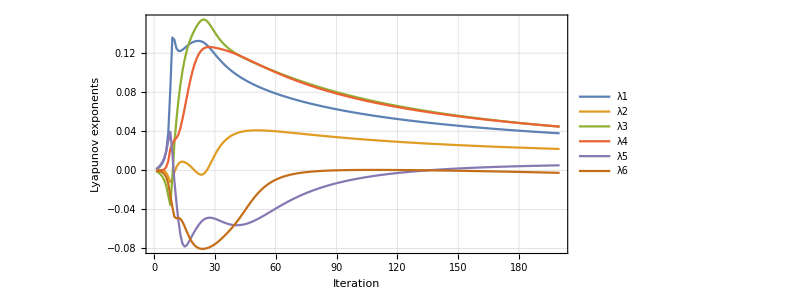

=== Detailed Convergence of Largest Exponent ===

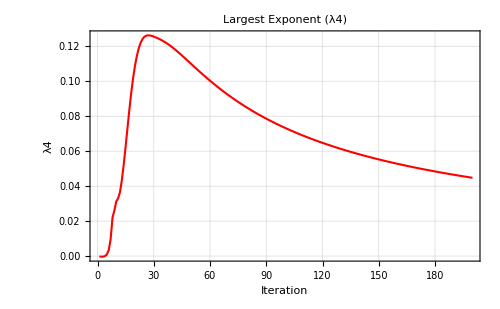

=== Final Lyapunov Spectrum ===

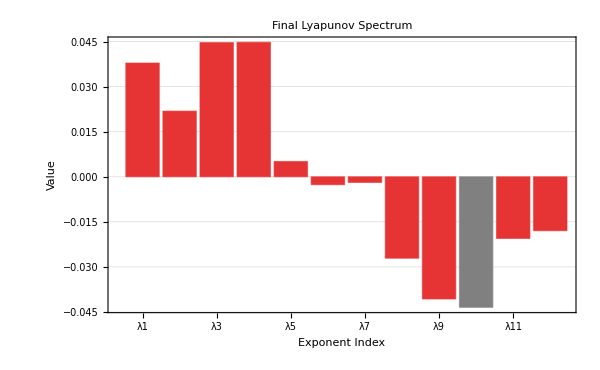

=== Symplectic Symmetry Check ===

λ_i + λ_{n+1-i} (should be near 0):

Pair 1: 0.019914

Pair 2: 0.00133376

Pair 3: 0.00120089

Pair 4: 0.00408883

Pair 5: -0.0220234

Pair 6: -0.00451415

Average deviation from 0: 0.00884584

=== Diagnostics ===

Initial energy (kinetic + potential):

E = 0.660935

Variation in last 10 λ₁ values: 0.00115782

⚠ λ₁ still showing significant variation - may need more iterations

```mathematica
(* ==========THREE-BODY LYAPUNOV EXPONENTS==========*)ClearAll["Global`*"];

(* ==========1. UTILITY FUNCTIONS==========*)
JacobianMtx[funs_List,vars_List]:=Outer[D,funs,vars]

RKStep[f_,y_,y0_,dt_]:=Module[{k1,k2,k3,k4},k1=dt N[f/. Thread[y->y0]];
k2=dt N[f/. Thread[y->y0+k1/2]];
k3=dt N[f/. Thread[y->y0+k2/2]];
k4=dt N[f/. Thread[y->y0+k3]];
y0+(k1+2 k2+2 k3+k4)/6]

RKPoint[f_List,y_List,y0_List,{t1_,dt_}]:=Nest[RKStep[f,y,#,N[dt]]&,N[y0],Round[N[t1/dt]]]

IntVarEq[F_List,DPhi_List,x_List,Phi_List,x0_List,Phi0_List,{t1_,dt_}]:=Module[{n,f,y,y0,yt},n=Length[x0];
f=Flatten[Join[F,DPhi]];
y=Flatten[Join[x,Phi]];
y0=Flatten[Join[x0,Phi0]];
yt=Nest[RKStep[f,y,#,N[dt]]&,N[y0],Round[N[t1/dt]]];
{First[#],Rest[#]}&@Partition[yt,n]]

(*Gram-Schmidt functions*)
prj[v1_,v2_]:=(v2.v1) v2/(v2.v2)
multiprj[v1_,vecs_]:=Plus@@Map[prj[v1,#]&,vecs]
GramSchm[vecs_]:=Fold[Join[#1,{#2-multiprj[#2,#1]}]&,{},vecs];

(* ==========2. THREE-BODY SYSTEM DEFINITION==========*)
(*Parameters*)
G=1.0;m1=1.0;m2=1.0;m3=1.0;
conv=0.1;
seed=105;

(*Initial conditions*)
SeedRandom[seed];
pos1={0,0};
vel1={0,10}*conv;
q2x=RandomReal[{5,20}];q2y=RandomReal[{0,10}];
pos2={q2x,q2y};vel2={-10,0}*conv;
q3x=RandomReal[{-10,0}];q3y=RandomReal[{5,20}];
pos3={q3x,q3y};vel3={0,0};

Print["=== Three-Body Initial Conditions (Seed ",seed,") ==="];
Print["Body 1: pos = ",pos1,", vel = ",vel1];
Print["Body 2: pos = ",pos2,", vel = ",vel2];
Print["Body 3: pos = ",pos3,", vel = ",vel3];
Print[""];

(* ==========3. FIRST-ORDER SYSTEM (12D)==========*)
(*Variables:x1,y1,vx1,vy1,x2,y2,vx2,vy2,x3,y3,vx3,vy3*)
x={x1,y1,vx1,vy1,x2,y2,vx2,vy2,x3,y3,vx3,vy3};
n=Length[x];  (*n=12*)

(*Distances for gravitational forces*)
r12=Sqrt[(x2-x1)^2+(y2-y1)^2];
r13=Sqrt[(x3-x1)^2+(y3-y1)^2];
r23=Sqrt[(x3-x2)^2+(y3-y2)^2];

(*Forces with regularization to avoid singularities*)
epsilon=10^-8;
force=1/(#^3+epsilon)&;  (*Regularized 1/r^3*)

(*Equations of motion:dx/dt=v,dv/dt=acceleration*)
F={vx1,(*x1'=vx1*)vy1,(*y1'=vy1*)G*m2*(x2-x1)*force[r12]+G*m3*(x3-x1)*force[r13],(*vx1'*)G*m2*(y2-y1)*force[r12]+G*m3*(y3-y1)*force[r13],(*vy1'*)vx2,(*x2'=vx2*)vy2,(*y2'=vy2*)G*m1*(x1-x2)*force[r12]+G*m3*(x3-x2)*force[r23],(*vx2'*)G*m1*(y1-y2)*force[r12]+G*m3*(y3-y2)*force[r23],(*vy2'*)vx3,(*x3'=vx3*)vy3,(*y3'=vy3*)G*m1*(x1-x3)*force[r13]+G*m2*(x2-x3)*force[r23],(*vx3'*)G*m1*(y1-y3)*force[r13]+G*m2*(y2-y3)*force[r23]   (*vy3'*)};

(* ==========4. JACOBIAN AND VARIATIONAL EQUATIONS==========*)
(*Compute Jacobian matrix symbolically*)
Phi=Array[b,{n,n}];
J=JacobianMtx[F,x];  (*12x12 Jacobian*)
DPhi=Flatten[Phi.Transpose[J]];  (*Variational equations*)

(*Initial conditions*)
x0=Flatten[{pos1,vel1,pos2,vel2,pos3,vel3}];
Phi0=IdentityMatrix[n];

Print["System dimension: n = ",n];
Print["Initial state (positions only):"];
Print["Body 1: {",x0[[1]],", ",x0[[2]],"}"];
Print["Body 2: {",x0[[5]],", ",x0[[6]],"}"];
Print["Body 3: {",x0[[9]],", ",x0[[10]],"}"];
Print[""];

(* ==========5. TEST INTEGRATION==========*)
Print["=== Testing integration for T = 1.0 ==="];
Ttest=1.0;
stepsize=0.1;
{xT,PhiT}=IntVarEq[F,DPhi,x,Phi,x0,Phi0,{Ttest,stepsize}];

Print["Position after t = ",Ttest,":"];
Print["Body 1: {",xT[[1]],", ",xT[[2]],"}"];
Print["Body 2: {",xT[[5]],", ",xT[[6]],"}"];
Print["Body 3: {",xT[[9]],", ",xT[[10]],"}"];

(*Quick Lyapunov test*)
u=Table[RandomReal[],{n}];
instantLambda=Log[Norm[PhiT.u]]/Ttest;
Print["Instantaneous λ estimate: ",instantLambda];
Print[""];

(* ==========6. MAIN LYAPUNOV COMPUTATION==========*)
(*Parameters*)
T=0.5;         (*Reorthonormalization time*)
stepsize=0.1;  (*Integration step*)
K=200;         (*Number of iterations-increased for better convergence*)

Print["=== Starting Lyapunov Computation ==="];
Print["T = ",T,", dt = ",stepsize,", K = ",K];
Print["Total integration time: ",K*T];
Print[""];

(*Initialize*)
PhiT=Phi0;
xT=x0;
s={};  (*Store norms for Gram-Schmidt*)
lambdaHistory={};
cumulativeLogs=Table[0.0,{n}];  (*Initialize cumulative logs*)

Monitor[Do[{xT,PhiT}=IntVarEq[F,DPhi,x,Phi,xT,PhiT,{T,stepsize}];
(*Gram-Schmidt reorthonormalization*)W=GramSchm[PhiT];
norms=Map[Norm,W];
(*Store norms*)s=Append[s,norms];
(*Reorthonormalize PhiT*)PhiT=W/norms;
(*Update cumulative logs and compute current LCEs*)cumulativeLogs=cumulativeLogs+Log[norms];
currentLCEs=cumulativeLogs/(i*T);(*i iterations of length T*)AppendTo[lambdaHistory,currentLCEs];
(*Progress*)If[Mod[i,20]==0,Print["Iteration ",i,"/",K,"  λ₁ = ",currentLCEs[[1]],"  λ₂ = ",currentLCEs[[2]],"  Max = ",Max[currentLCEs]]];,{i,K}],ProgressIndicator[i,{1,K}]];

Print[""];
Print["=== Computation Complete ==="];

(* ==========7. FINAL RESULTS==========*)
finalLCEs=Last[lambdaHistory];
Print["\nFinal Lyapunov Exponents (after ",K," iterations):"];
For[i=1,i<=Min[12,Length[finalLCEs]],i++,Print["λ",i," = ",finalLCEs[[i]]]];

Print[""];
Print["Largest λ (chaos strength): ",Max[finalLCEs]];
Print["Number of positive exponents: ",Count[finalLCEs,x_/;x>0.001]];
Print["Sum of λ's (should be ~0 for Hamiltonian): ",Total[finalLCEs]];

(*Check for chaos*)
maxLCE=Max[finalLCEs];
If[maxLCE>0.01,Print["\n✓ SYSTEM IS CHAOTIC (positive Lyapunov exponent > 0.01)"],If[maxLCE>0,Print["\n⚠ System shows weak chaos (positive but small exponent)"],Print["\n✗ System appears regular (no positive exponent)"]]];

(* ==========8. PLOTTING==========*)
(*8.1 Convergence plot of first 6 exponents*)
Print["\n=== Convergence Plot (First 6 Exponents) ==="];
If[Length[lambdaHistory]>0,convData=Transpose[lambdaHistory][[1;;6]];(*First 6 exponents*)convPlot=ListLinePlot[convData,PlotLegends->Placed[LineLegend[Table[Style["λ"<>ToString[i],FontSize->12],{i,6}],LegendFunction->(Framed[#,RoundingRadius->0]&)],Right],Frame->True,FrameStyle->Directive[Black,Thickness[0.002]],FrameLabel->{Style["Iteration",Italic,FontSize->14],Style["Lyapunov exponents",Italic,FontSize->14]},GridLines->Automatic,GridLinesStyle->LightGray,ImageSize->600,AspectRatio->1/2,PlotRange->{{0,200},All}];

Print[convPlot];];

(*8.2 Detailed convergence of largest exponent*)
Print["\n=== Detailed Convergence of Largest Exponent ==="];
largestIndex=First[Ordering[finalLCEs,-1]];
largestExpData=Transpose[lambdaHistory][[largestIndex]];
plotLargest=ListPlot[largestExpData,Joined->True,Frame->True,FrameLabel->{"Iteration","λ"<>ToString[largestIndex]},PlotLabel->Style["Largest Exponent (λ"<>ToString[largestIndex]<>")",14],GridLines->Automatic,ImageSize->500,PlotStyle->{Red,Thickness[0.003]}];
Print[plotLargest];

(*8.3 Final spectrum bar chart*)
Print["\n=== Final Lyapunov Spectrum ==="];
spectrumPlot=BarChart[finalLCEs,ChartLabels->Table["λ"<>ToString[i],{i,Length[finalLCEs]}],Frame->True,FrameLabel->{"Exponent Index","Value"},PlotLabel->Style["Final Lyapunov Spectrum",16,Bold],GridLines->Automatic,ImageSize->600,ColorFunction->Function[{height},If[height>0.001,RGBColor[0.9,0.2,0.2],If[height<-0.001,RGBColor[0.2,0.2,0.9],RGBColor[0.5,0.5,0.5]]]],ChartStyle->"TemperatureMap"];
Print[spectrumPlot];

(*8.4 Symplectic symmetry check:λ_i+λ_{n+1-i} should be~0*)
Print["\n=== Symplectic Symmetry Check ==="];
If[EvenQ[n],sympPairs=Table[finalLCEs[[i]]+finalLCEs[[n+1-i]],{i,n/2}];
Print["λ_i + λ_{n+1-i} (should be near 0):"];
For[i=1,i<=Length[sympPairs],i++,Print["Pair ",i,": ",sympPairs[[i]]]];
Print["Average deviation from 0: ",Mean[Abs[sympPairs]]];];


(*
(*8.5 Trajectory plot (optional)*)
Print["\n=== Optional: Short Trajectory Plot ==="];
trajSteps=1000;
trajDT=0.01;
trajPoints=NestList[RKStep[F,x,#,trajDT]&,x0,trajSteps];
traj1=trajPoints[[All,{1,2}]];
traj2=trajPoints[[All,{5,6}]];
traj3=trajPoints[[All,{9,10}]];

trajPlot=ListLinePlot[{traj1,traj2,traj3},PlotStyle->{{Blue,Thickness[0.002]},{Red,Thickness[0.002]},{Green,Thickness[0.002]}},Frame->True,FrameLabel->{"x","y"},PlotLabel->Style["Trajectories (first "<>ToString[trajSteps*trajDT]<>" time units)",14],AspectRatio->1,ImageSize->500,PlotLegends->{"Body 1","Body 2","Body 3"}];
Print[trajPlot];


*)

(* ==========9. DIAGNOSTICS==========*)
Print["\n=== Diagnostics ==="];
Print["Initial energy (kinetic + potential):"];
(*Compute initial energy*)
r12init=Norm[pos2-pos1];
r13init=Norm[pos3-pos1];
r23init=Norm[pos3-pos2];
kinetic=0.5*m1*Norm[vel1]^2+0.5*m2*Norm[vel2]^2+0.5*m3*Norm[vel3]^2;
potential=-G*(m1*m2/r12init+m1*m3/r13init+m2*m3/r23init);
energyInit=kinetic+potential;
Print["E = ",energyInit];

(*Check if exponents are converging*)
If[Length[lambdaHistory]>10,lastValues=Take[Transpose[lambdaHistory][[1]],-10];
variation=Max[lastValues]-Min[lastValues];
Print["Variation in last 10 λ₁ values: ",variation];
If[variation<0.01*Abs[Mean[lastValues]],Print["✓ λ₁ appears to be converging"],Print["⚠ λ₁ still showing significant variation - may need more iterations"]];];
```

=== Three-Body Initial Conditions (Seed 121) ===

Body 1: pos = {0,0}, vel = {0.,1.}

Body 2: pos = {6.36238,1.94288}, vel = {-1.,0.}

Body 3: pos = {-7.03238,13.9367}, vel = {0,0}

System dimension: n = 12

Initial state (positions only):

Body 1: {0, 0}

Body 2: {6.36238, 1.94288}

Body 3: {-7.03238, 13.9367}

=== Testing integration for T = 1.0 ===

Position after t = 1.:

Body 1: {0.0115259, 1.00518}

Body 2: {5.3487, 1.94067}

Body 3: {-7.03023, 13.9337}

Instantaneous λ estimate: 1.088

=== Starting Lyapunov Computation ===

T = 0.5, dt = 0.1, K = 200

Total integration time: 100.

Iteration 20/200  λ₁ = 0.0643524  λ₂ = 0.00355354  Max = 0.118534

Iteration 40/200  λ₁ = 0.0626961  λ₂ = -0.00301792  Max = 0.121956

Iteration 60/200  λ₁ = 0.0540867  λ₂ = 0.00118865  Max = 0.105876

Iteration 80/200  λ₁ = 0.0466985  λ₂ = 0.00660135  Max = 0.091426

Iteration 100/200  λ₁ = 0.0412606  λ₂ = 0.009795  Max = 0.0799354

Iteration 120/200  λ₁ = 0.0371244  λ₂ = 0.0114648  Max = 0.0708763

Iteration 140/200  λ₁ = 0.0338554  λ₂ = 0.0122772  Max = 0.0636478

Iteration 160/200  λ₁ = 0.0311929  λ₂ = 0.0126119  Max = 0.057781

Iteration 180/200  λ₁ = 0.0289735  λ₂ = 0.012676  Max = 0.0529373

Iteration 200/200  λ₁ = 0.0270895  λ₂ = 0.0125849  Max = 0.0488752

=== Computation Complete ===

Final Lyapunov Exponents (after 200 iterations):

λ1 = 0.0270895

λ2 = 0.0125849

λ3 = 0.0488752

λ4 = 0.0437355

λ5 = -0.001318

λ6 = -0.000826304

λ7 = -0.00488252

λ8 = -0.0179023

λ9 = -0.039591

λ10 = -0.0419573

λ11 = -0.0162268

λ12 = -0.00958093

Largest λ (chaos strength): 0.0488752

Number of positive exponents: 4

Sum of λ's (should be ~0 for Hamiltonian): -1.85566×10^-10

✓ SYSTEM IS CHAOTIC (positive Lyapunov exponent > 0.01)

=== Convergence Plot (First 6 Exponents) ===

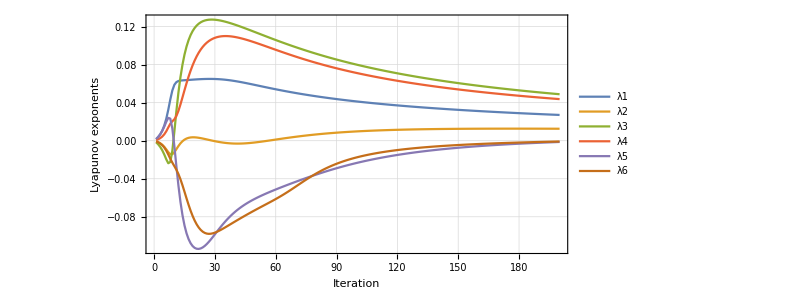

=== Detailed Convergence of Largest Exponent ===

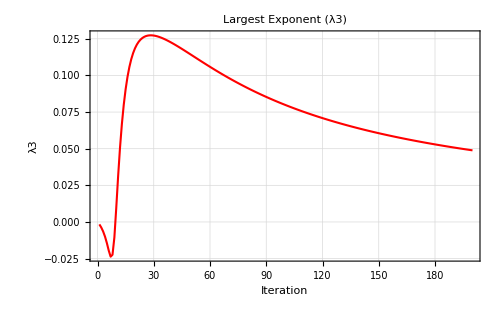

=== Final Lyapunov Spectrum ===

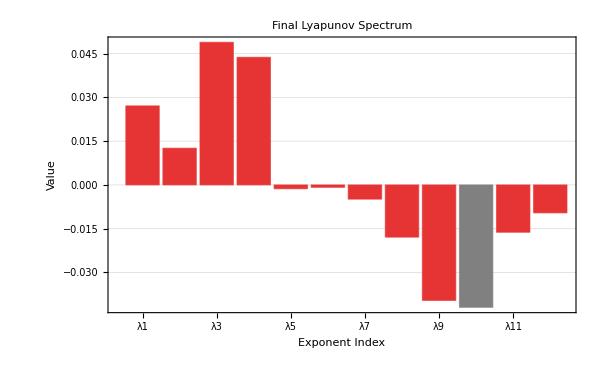

=== Symplectic Symmetry Check ===

λ_i + λ_{n+1-i} (should be near 0):

Pair 1: 0.0175086

Pair 2: -0.00364188

Pair 3: 0.00691789

Pair 4: 0.00414451

Pair 5: -0.0192203

Pair 6: -0.00570883

Average deviation from 0: 0.00952367

=== Diagnostics ===

Initial energy (kinetic + potential):

E = 0.730001

Variation in last 10 λ₁ values: 0.000811649

⚠ λ₁ still showing significant variation - may need more iterations

```mathematica
(* ==========THREE-BODY LYAPUNOV EXPONENTS==========*)ClearAll["Global`*"];

(* ==========1. UTILITY FUNCTIONS==========*)
JacobianMtx[funs_List,vars_List]:=Outer[D,funs,vars]

RKStep[f_,y_,y0_,dt_]:=Module[{k1,k2,k3,k4},k1=dt N[f/. Thread[y->y0]];
k2=dt N[f/. Thread[y->y0+k1/2]];
k3=dt N[f/. Thread[y->y0+k2/2]];
k4=dt N[f/. Thread[y->y0+k3]];
y0+(k1+2 k2+2 k3+k4)/6]

RKPoint[f_List,y_List,y0_List,{t1_,dt_}]:=Nest[RKStep[f,y,#,N[dt]]&,N[y0],Round[N[t1/dt]]]

IntVarEq[F_List,DPhi_List,x_List,Phi_List,x0_List,Phi0_List,{t1_,dt_}]:=Module[{n,f,y,y0,yt},n=Length[x0];
f=Flatten[Join[F,DPhi]];
y=Flatten[Join[x,Phi]];
y0=Flatten[Join[x0,Phi0]];
yt=Nest[RKStep[f,y,#,N[dt]]&,N[y0],Round[N[t1/dt]]];
{First[#],Rest[#]}&@Partition[yt,n]]

(*Gram-Schmidt functions*)
prj[v1_,v2_]:=(v2.v1) v2/(v2.v2)
multiprj[v1_,vecs_]:=Plus@@Map[prj[v1,#]&,vecs]
GramSchm[vecs_]:=Fold[Join[#1,{#2-multiprj[#2,#1]}]&,{},vecs];

(* ==========2. THREE-BODY SYSTEM DEFINITION==========*)
(*Parameters*)
G=1.0;m1=1.0;m2=1.0;m3=1.0;
conv=0.1;
seed=121;

(*Initial conditions*)
SeedRandom[seed];
pos1={0,0};
vel1={0,10}*conv;
q2x=RandomReal[{5,20}];q2y=RandomReal[{0,10}];
pos2={q2x,q2y};vel2={-10,0}*conv;
q3x=RandomReal[{-10,0}];q3y=RandomReal[{5,20}];
pos3={q3x,q3y};vel3={0,0};

Print["=== Three-Body Initial Conditions (Seed ",seed,") ==="];
Print["Body 1: pos = ",pos1,", vel = ",vel1];
Print["Body 2: pos = ",pos2,", vel = ",vel2];
Print["Body 3: pos = ",pos3,", vel = ",vel3];
Print[""];

(* ==========3. FIRST-ORDER SYSTEM (12D)==========*)
(*Variables:x1,y1,vx1,vy1,x2,y2,vx2,vy2,x3,y3,vx3,vy3*)
x={x1,y1,vx1,vy1,x2,y2,vx2,vy2,x3,y3,vx3,vy3};
n=Length[x];  (*n=12*)

(*Distances for gravitational forces*)
r12=Sqrt[(x2-x1)^2+(y2-y1)^2];
r13=Sqrt[(x3-x1)^2+(y3-y1)^2];
r23=Sqrt[(x3-x2)^2+(y3-y2)^2];

(*Forces with regularization to avoid singularities*)
epsilon=10^-8;
force=1/(#^3+epsilon)&;  (*Regularized 1/r^3*)

(*Equations of motion:dx/dt=v,dv/dt=acceleration*)
F={vx1,(*x1'=vx1*)vy1,(*y1'=vy1*)G*m2*(x2-x1)*force[r12]+G*m3*(x3-x1)*force[r13],(*vx1'*)G*m2*(y2-y1)*force[r12]+G*m3*(y3-y1)*force[r13],(*vy1'*)vx2,(*x2'=vx2*)vy2,(*y2'=vy2*)G*m1*(x1-x2)*force[r12]+G*m3*(x3-x2)*force[r23],(*vx2'*)G*m1*(y1-y2)*force[r12]+G*m3*(y3-y2)*force[r23],(*vy2'*)vx3,(*x3'=vx3*)vy3,(*y3'=vy3*)G*m1*(x1-x3)*force[r13]+G*m2*(x2-x3)*force[r23],(*vx3'*)G*m1*(y1-y3)*force[r13]+G*m2*(y2-y3)*force[r23]   (*vy3'*)};

(* ==========4. JACOBIAN AND VARIATIONAL EQUATIONS==========*)
(*Compute Jacobian matrix symbolically*)
Phi=Array[b,{n,n}];
J=JacobianMtx[F,x];  (*12x12 Jacobian*)
DPhi=Flatten[Phi.Transpose[J]];  (*Variational equations*)

(*Initial conditions*)
x0=Flatten[{pos1,vel1,pos2,vel2,pos3,vel3}];
Phi0=IdentityMatrix[n];

Print["System dimension: n = ",n];
Print["Initial state (positions only):"];
Print["Body 1: {",x0[[1]],", ",x0[[2]],"}"];
Print["Body 2: {",x0[[5]],", ",x0[[6]],"}"];
Print["Body 3: {",x0[[9]],", ",x0[[10]],"}"];
Print[""];

(* ==========5. TEST INTEGRATION==========*)
Print["=== Testing integration for T = 1.0 ==="];
Ttest=1.0;
stepsize=0.1;
{xT,PhiT}=IntVarEq[F,DPhi,x,Phi,x0,Phi0,{Ttest,stepsize}];

Print["Position after t = ",Ttest,":"];
Print["Body 1: {",xT[[1]],", ",xT[[2]],"}"];
Print["Body 2: {",xT[[5]],", ",xT[[6]],"}"];
Print["Body 3: {",xT[[9]],", ",xT[[10]],"}"];

(*Quick Lyapunov test*)
u=Table[RandomReal[],{n}];
instantLambda=Log[Norm[PhiT.u]]/Ttest;
Print["Instantaneous λ estimate: ",instantLambda];
Print[""];

(* ==========6. MAIN LYAPUNOV COMPUTATION==========*)
(*Parameters*)
T=0.5;         (*Reorthonormalization time*)
stepsize=0.1;  (*Integration step*)
K=200;         (*Number of iterations-increased for better convergence*)

Print["=== Starting Lyapunov Computation ==="];
Print["T = ",T,", dt = ",stepsize,", K = ",K];
Print["Total integration time: ",K*T];
Print[""];

(*Initialize*)
PhiT=Phi0;
xT=x0;
s={};  (*Store norms for Gram-Schmidt*)
lambdaHistory={};
cumulativeLogs=Table[0.0,{n}];  (*Initialize cumulative logs*)

Monitor[Do[{xT,PhiT}=IntVarEq[F,DPhi,x,Phi,xT,PhiT,{T,stepsize}];
(*Gram-Schmidt reorthonormalization*)W=GramSchm[PhiT];
norms=Map[Norm,W];
(*Store norms*)s=Append[s,norms];
(*Reorthonormalize PhiT*)PhiT=W/norms;
(*Update cumulative logs and compute current LCEs*)cumulativeLogs=cumulativeLogs+Log[norms];
currentLCEs=cumulativeLogs/(i*T);(*i iterations of length T*)AppendTo[lambdaHistory,currentLCEs];
(*Progress*)If[Mod[i,20]==0,Print["Iteration ",i,"/",K,"  λ₁ = ",currentLCEs[[1]],"  λ₂ = ",currentLCEs[[2]],"  Max = ",Max[currentLCEs]]];,{i,K}],ProgressIndicator[i,{1,K}]];

Print[""];
Print["=== Computation Complete ==="];

(* ==========7. FINAL RESULTS==========*)
finalLCEs=Last[lambdaHistory];
Print["\nFinal Lyapunov Exponents (after ",K," iterations):"];
For[i=1,i<=Min[12,Length[finalLCEs]],i++,Print["λ",i," = ",finalLCEs[[i]]]];

Print[""];
Print["Largest λ (chaos strength): ",Max[finalLCEs]];
Print["Number of positive exponents: ",Count[finalLCEs,x_/;x>0.001]];
Print["Sum of λ's (should be ~0 for Hamiltonian): ",Total[finalLCEs]];

(*Check for chaos*)
maxLCE=Max[finalLCEs];
If[maxLCE>0.01,Print["\n✓ SYSTEM IS CHAOTIC (positive Lyapunov exponent > 0.01)"],If[maxLCE>0,Print["\n⚠ System shows weak chaos (positive but small exponent)"],Print["\n✗ System appears regular (no positive exponent)"]]];

(* ==========8. PLOTTING==========*)
(*8.1 Convergence plot of first 6 exponents*)
Print["\n=== Convergence Plot (First 6 Exponents) ==="];
If[Length[lambdaHistory]>0,convData=Transpose[lambdaHistory][[1;;6]];(*First 6 exponents*)convPlot=ListLinePlot[convData,PlotLegends->Placed[LineLegend[Table[Style["λ"<>ToString[i],FontSize->12],{i,6}],LegendFunction->(Framed[#,RoundingRadius->0]&)],Right],Frame->True,FrameStyle->Directive[Black,Thickness[0.002]],FrameLabel->{Style["Iteration",Italic,FontSize->14],Style["Lyapunov exponents",Italic,FontSize->14]},GridLines->Automatic,GridLinesStyle->LightGray,ImageSize->600,AspectRatio->1/2,PlotRange->{{0,200},All}];

Print[convPlot];];

(*8.2 Detailed convergence of largest exponent*)
Print["\n=== Detailed Convergence of Largest Exponent ==="];
largestIndex=First[Ordering[finalLCEs,-1]];
largestExpData=Transpose[lambdaHistory][[largestIndex]];
plotLargest=ListPlot[largestExpData,Joined->True,Frame->True,FrameLabel->{"Iteration","λ"<>ToString[largestIndex]},PlotLabel->Style["Largest Exponent (λ"<>ToString[largestIndex]<>")",14],GridLines->Automatic,ImageSize->500,PlotStyle->{Red,Thickness[0.003]}];
Print[plotLargest];

(*8.3 Final spectrum bar chart*)
Print["\n=== Final Lyapunov Spectrum ==="];
spectrumPlot=BarChart[finalLCEs,ChartLabels->Table["λ"<>ToString[i],{i,Length[finalLCEs]}],Frame->True,FrameLabel->{"Exponent Index","Value"},PlotLabel->Style["Final Lyapunov Spectrum",16,Bold],GridLines->Automatic,ImageSize->600,ColorFunction->Function[{height},If[height>0.001,RGBColor[0.9,0.2,0.2],If[height<-0.001,RGBColor[0.2,0.2,0.9],RGBColor[0.5,0.5,0.5]]]],ChartStyle->"TemperatureMap"];
Print[spectrumPlot];

(*8.4 Symplectic symmetry check:λ_i+λ_{n+1-i} should be~0*)
Print["\n=== Symplectic Symmetry Check ==="];
If[EvenQ[n],sympPairs=Table[finalLCEs[[i]]+finalLCEs[[n+1-i]],{i,n/2}];
Print["λ_i + λ_{n+1-i} (should be near 0):"];
For[i=1,i<=Length[sympPairs],i++,Print["Pair ",i,": ",sympPairs[[i]]]];
Print["Average deviation from 0: ",Mean[Abs[sympPairs]]];];


(*
(*8.5 Trajectory plot (optional)*)
Print["\n=== Optional: Short Trajectory Plot ==="];
trajSteps=1000;
trajDT=0.01;
trajPoints=NestList[RKStep[F,x,#,trajDT]&,x0,trajSteps];
traj1=trajPoints[[All,{1,2}]];
traj2=trajPoints[[All,{5,6}]];
traj3=trajPoints[[All,{9,10}]];

trajPlot=ListLinePlot[{traj1,traj2,traj3},PlotStyle->{{Blue,Thickness[0.002]},{Red,Thickness[0.002]},{Green,Thickness[0.002]}},Frame->True,FrameLabel->{"x","y"},PlotLabel->Style["Trajectories (first "<>ToString[trajSteps*trajDT]<>" time units)",14],AspectRatio->1,ImageSize->500,PlotLegends->{"Body 1","Body 2","Body 3"}];
Print[trajPlot];


*)

(* ==========9. DIAGNOSTICS==========*)
Print["\n=== Diagnostics ==="];
Print["Initial energy (kinetic + potential):"];
(*Compute initial energy*)
r12init=Norm[pos2-pos1];
r13init=Norm[pos3-pos1];
r23init=Norm[pos3-pos2];
kinetic=0.5*m1*Norm[vel1]^2+0.5*m2*Norm[vel2]^2+0.5*m3*Norm[vel3]^2;
potential=-G*(m1*m2/r12init+m1*m3/r13init+m2*m3/r23init);
energyInit=kinetic+potential;
Print["E = ",energyInit];

(*Check if exponents are converging*)
If[Length[lambdaHistory]>10,lastValues=Take[Transpose[lambdaHistory][[1]],-10];
variation=Max[lastValues]-Min[lastValues];
Print["Variation in last 10 λ₁ values: ",variation];
If[variation<0.01*Abs[Mean[lastValues]],Print["✓ λ₁ appears to be converging"],Print["⚠ λ₁ still showing significant variation - may need more iterations"]];];
```